# qTraj Workbook

### General setup

```mathematica
wd =SetDirectory@NotebookDirectory[]
```

/Users/mstrick6/Documents/code/qtraj-nlo/mathematica

```mathematica
ImportSnaps[dir_] := Module[{fNames,fNamesSort,fNamesSorted,rawData,absData},
fNames=FileNames[wd<>"/../"<>dir<>"/snapshot_*"];
fNamesSort=Partition[Riffle[ToExpression[StringSplit[fNames,{"_","."}][[All,4]]],fNames],2] ;
fNamesSorted = Sort[fNamesSort,#1[[1]]<#2[[1]]&][[All,2]];
rawData=ParallelTable[Import[fNamesSorted[[i]],"Table"],{i,1,Length[fNamesSorted]}];
Table[rawData[[snap]][[All,{1,2}]],{snap,1,Length[rawData]}]
]
```

```mathematica
(*splitSpace[x_] := StringSplit[x," "]; 
rawParams = Import[wd<>"/../input/params.txt"];
paramsLines= StringSplit[rawParams,"\n"];
params=splitSpace/@Select[paramsLines,StringLength[#]>0 &];
paramNames = params[[All,1]]*)
```

### Plot setup

```mathematica
SetOptions[Plot,Frame->True,Axes->False,ImageSize->450,AspectRatio->0.7,BaseStyle->18,FrameStyle->AbsoluteThickness[1]];
SetOptions[ListPlot,Frame->True,Axes->False,ImageSize->450,AspectRatio->0.7,BaseStyle->18,FrameStyle->AbsoluteThickness[1]];
SetOptions[LogPlot,Frame->True,Axes->False,ImageSize->450,AspectRatio->0.7,BaseStyle->18,FrameStyle->AbsoluteThickness[1]];
SetOptions[LogLogPlot,Frame->True,Axes->False,ImageSize->450,AspectRatio->0.7,BaseStyle->18,FrameStyle->AbsoluteThickness[1]];
SetOptions[LogLinearPlot,Frame->True,Axes->False,ImageSize->450,AspectRatio->0.7,BaseStyle->18,FrameStyle->AbsoluteThickness[1]];
SetOptions[ComplexPlot,Frame->True,Axes->False,ImageSize->450,AspectRatio->1,BaseStyle->18,FrameStyle->AbsoluteThickness[1]];
SetOptions[ListLogPlot,Frame->True,Axes->False,ImageSize->450,AspectRatio->0.7,BaseStyle->18,FrameStyle->AbsoluteThickness[1]];
SetOptions[ListLogLogPlot,Frame->True,Axes->False,ImageSize->450,AspectRatio->0.7,BaseStyle->18,FrameStyle->AbsoluteThickness[1]];
```

## Single tests

### S-wave (n=0)

```mathematica
absData0 = ImportSnaps["output-0"];
absData1 = ImportSnaps["output-1"];
absData2 = ImportSnaps["output-2"];
```

```mathematica
step = 1;plots = ParallelTable[ListPlot[{absData0[[i]],absData1[[i]],absData2[[i]]},Joined->True,ImageSize->500,PlotRange->{{0,10},{0,1}},Frame->True,PlotStyle->{Thick,Thick,{Thick,Dashed}},PlotLegends->Placed[LineLegend[{"LO Suzuki-Trotter","LO Crank-Nicholson","NLO Crank-Nicholson"}],{Right,Top}]],{i,1,Length[absData0],step}];
```

```mathematica
Manipulate[plots[[i]],{i,1,Length[plots],1}]
```

Part::partd: Part specification plots⟦1⟧ is longer than depth of object.

```mathematica
Export[wd<>"/s-wave.mp4",plots];
```

### Delta Function

```mathematica
absData0 = ImportSnaps["output-0"];
absData1 = ImportSnaps["output-1"];
absData2 = ImportSnaps["output-2"];
```

```mathematica
step = 1;plots = ParallelTable[ListPlot[{absData0[[i]],absData1[[i]],absData2[[i]]},Joined->True,ImageSize->500,PlotRange->All,Frame->True,PlotStyle->{Thick,Thick,{Thick,Dashed}},PlotLegends->Placed[LineLegend[{"LO Suzuki-Trotter","LO Crank-Nicholson","NLO Crank-Nicholson"}],{Right,Top}]],{i,1,Length[absData0],step}];
```

```mathematica
Manipulate[plots[[i]],{i,1,Length[plots],1}]
```

Part::partw: Part 1 of {} does not exist.

Part::partd: Part specification plots⟦17⟧ is longer than depth of object.

```mathematica
Export[wd<>"/delta.mp4",plots];
```

### S-wave with Jumps

```mathematica
absData0 = ImportSnaps["output-0"];
absData1 = ImportSnaps["output-1"];
absData2= ImportSnaps["output-2"];
```

```mathematica
step=1;plots = ParallelTable[ListPlot[{absData0[[i]],absData1[[i]](*,absData2[[i]]*)},Joined->True,ImageSize->500,PlotRange->All,Frame->True,PlotStyle->{Thick,Thick,{Thick,Dashed}},PlotLegends->Placed[LineLegend[{"LO Suzuki-Trotter","LO Crank-Nicholson","NLO Crank-Nicholson"}],{Right,Top}]],{i,1,Length[absData0],step}];
```

```mathematica
Manipulate[plots[[i]],{i,1,Length[plots],1}]
```

Part::partd: Part specification plots⟦1⟧ is longer than depth of object.

```mathematica
Export[wd<>"/swave-jumps.mp4",plots];
```

### Delta with Jumps

```mathematica
absData0 = ImportSnaps["output-0"];
absData1 = ImportSnaps["output-1"];
absData2= ImportSnaps["output-2"];
{Length[absData0],Length[absData1],Length[absData2]}
len = Min[{Length[absData0],Length[absData1],Length[absData2]}];
```

{154,154,154}

```mathematica
step=1;plots = ParallelTable[ListPlot[{absData0[[i]],absData1[[i]],absData2[[i]]},Joined->True,ImageSize->500,PlotRange->{0,1},Frame->True,PlotStyle->{Thick,Thick,{Thick,Dashed}},PlotLegends->Placed[LineLegend[{"LO Suzuki-Trotter","LO Crank-Nicholson","NLO Crank-Nicholson"}],{Right,Top}]],{i,1,len,step}];
```

```mathematica
Manipulate[plots[[i]],{i,1,Length[plots],1}]
```

Part::partd: Part specification plots⟦1⟧ is longer than depth of object.

```mathematica
Export[wd<>"/delta-jumps.mp4",plots];
```

## Summary plots - Delta Heff

```mathematica
summaryData0=Import[wd<>"/../output-0/summary.tsv"];
summaryData1=Import[wd<>"/../output-1/summary.tsv"];
summaryData2=Import[wd<>"/../output-2/summary.tsv"];
grabColumn[x_,n_] := Transpose[{x[[All,1]],x[[All,n]]}]
grabNormedColumn[x_,n_] := Transpose[{x[[All,1]],x[[All,n]]/x[[All,n]][[1]]}]
```

```mathematica
makePlot[col_,label_]:=ListPlot[{grabColumn[summaryData0,col],grabColumn[summaryData1,col],grabColumn[summaryData2,col]},Joined->True,PlotStyle->{Thick,Thick,{Thick,Dashed}},PlotLegends->Placed[LineLegend[{"LO Suzuki-Trotter","LO Crank-Nicholson","NLO Crank-Nicholson"},LabelStyle->Directive[FontSize->14]],{Right,Top}],FrameLabel->{"τ [fm]",label},PlotRange->All]
makeLogPlot[col_,label_]:=ListLogPlot[{grabColumn[summaryData0,col],grabColumn[summaryData1,col],grabColumn[summaryData2,col]},Joined->True,PlotStyle->{Thick,Thick,{Thick,Dashed}},PlotLegends->Placed[LineLegend[{"LO Suzuki-Trotter","LO Crank-Nicholson","NLO Crank-Nicholson"},LabelStyle->Directive[FontSize->14]],{Right,Top}],FrameLabel->{"τ [fm]",label},PlotRange->All]
makeNormedPlot[col_,label_]:=ListLogPlot[{grabNormedColumn[summaryData0,col],grabNormedColumn[summaryData1,col],grabNormedColumn[summaryData2,col]},Joined->True,PlotStyle->{Thick,Thick,{Thick,Dashed}},PlotLegends->Placed[LineLegend[{"LO Suzuki-Trotter","LO Crank-Nicholson","NLO Crank-Nicholson"},LabelStyle->Directive[FontSize->14]],{Right,Top}],FrameLabel->{"τ [fm]",label}]
```

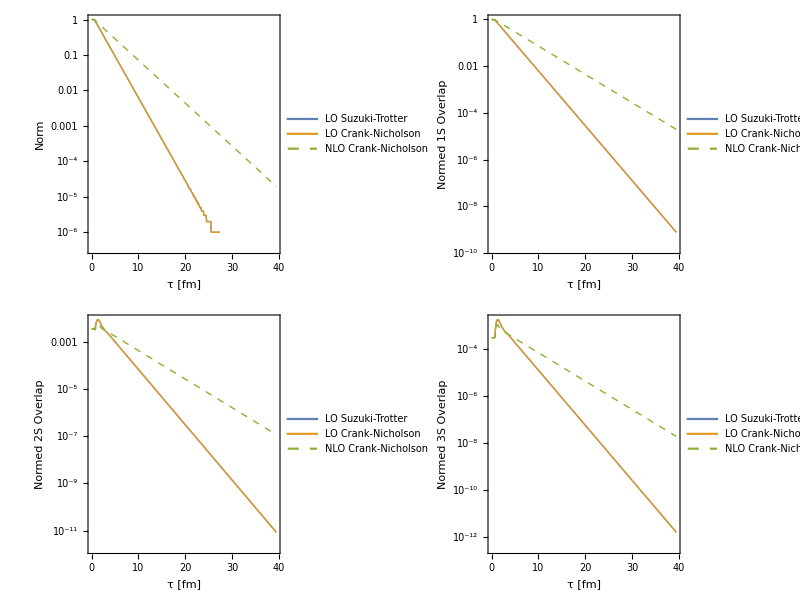

```mathematica
Grid[{{makeLogPlot[2,"Norm"],makeLogPlot[5,"Normed 1S Overlap"]},{makeLogPlot[6,"Normed 2S Overlap"],makeLogPlot[8,"Normed 3S Overlap"]}}]
```

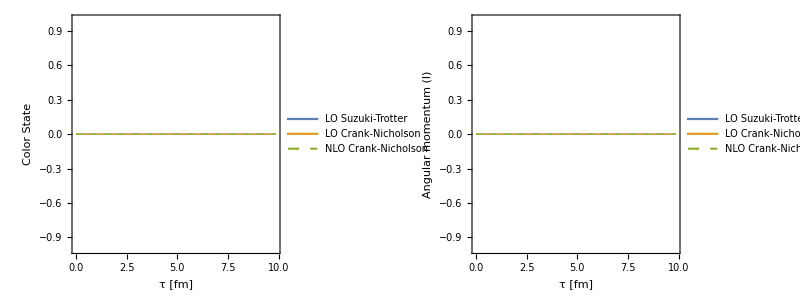

```mathematica
Grid[{{makePlot[3,"Color State"],makePlot[4,"Angular momentum (l)"]}}]
```

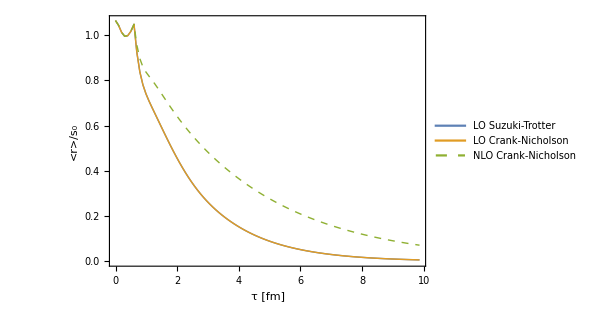

```mathematica
makePlot[11,"<r>/s_0"]
```

### Ratios

```mathematica
makeRatio[x_,n1_,n2_]:=Transpose[{grabColumn[x,n1][[All,1]],grabColumn[x,n1][[All,2]]/grabColumn[x,n2][[All,2]]}]
```

```mathematica
makeRatio[summaryData0,6,5][[-1]]
makeRatio[summaryData2,6,5][[-1]]
```

{39.4654,0.0108576}

{39.4654,0.00597506}

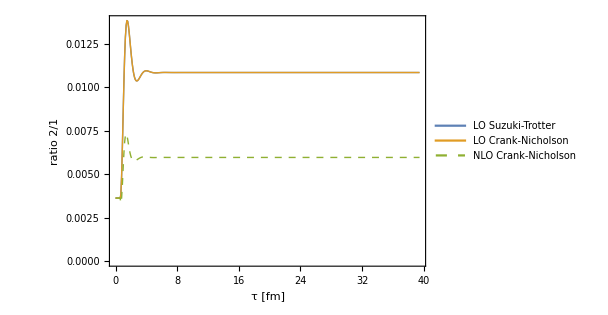
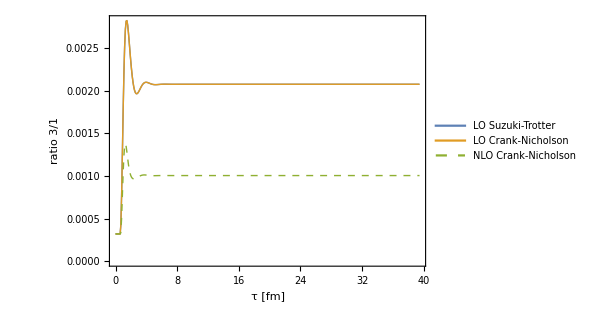
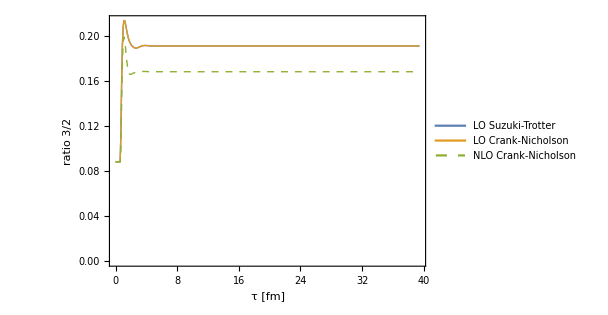
-Graphics- | -Graphics-
-Graphics- |

```mathematica
Grid[{{ListPlot[{makeRatio[summaryData0,6,5],makeRatio[summaryData1,6,5],makeRatio[summaryData2,6,5]},Joined->True,PlotStyle->{Thick,Thick,{Thick,Dashed}},PlotLegends->Placed[LineLegend[{"LO Suzuki-Trotter","LO Crank-Nicholson","NLO Crank-Nicholson"},LabelStyle->Directive[FontSize->14]],{Right,Top}],FrameLabel->{"τ [fm]","ratio 2/1"},PlotRange->All],
ListPlot[{makeRatio[summaryData0,8,5],makeRatio[summaryData1,8,5],makeRatio[summaryData2,8,5]},Joined->True,PlotStyle->{Thick,Thick,{Thick,Dashed}},PlotLegends->Placed[LineLegend[{"LO Suzuki-Trotter","LO Crank-Nicholson","NLO Crank-Nicholson"},LabelStyle->Directive[FontSize->14]],{Right,Top}],FrameLabel->{"τ [fm]","ratio 3/1"},PlotRange->All]},{
ListPlot[{makeRatio[summaryData0,8,6],makeRatio[summaryData1,8,6],makeRatio[summaryData2,8,6]},Joined->True,PlotStyle->{Thick,Thick,{Thick,Dashed}},PlotLegends->Placed[LineLegend[{"LO Suzuki-Trotter","LO Crank-Nicholson","NLO Crank-Nicholson"},LabelStyle->Directive[FontSize->14]],{Right,Bottom}],FrameLabel->{"τ [fm]","ratio 3/2"},PlotRange->All]}}]
```

## Summary plots - Delta with jumps

```mathematica
summaryData0=Import[wd<>"/../output-0/summary.tsv"];
summaryData1=Import[wd<>"/../output-0/summary.tsv"];
summaryData2=Import[wd<>"/../output-2/summary.tsv"];
grabColumn[x_,n_] := Transpose[{x[[All,1]],x[[All,n]]}]
grabNormedColumn[x_,n_] := Transpose[{x[[All,1]],x[[All,n]]/x[[All,n]][[1]]}]
```

```mathematica
Length[summaryData0]
Length[summaryData1]
Length[summaryData2]
```

350

350

350

```mathematica
(*ListLogPlot[Abs[(summaryData0[[All,5]]-summaryData1[[All,5]])],PlotMarkers->"OpenMarkers"]*)
```

```mathematica
(*ListLogPlot[Abs[Total/@(summaryData0[[All,5;;-1]]-summaryData1[[All,5;;-1]])]]*)
```

```mathematica
keyVal =0.600012;
grabTrajectoryColumn[x_,n_,m_] := Module[{pos,data},
data=grabColumn[x,n];
pos=Join[Position[x[[All,1]],keyVal]//Flatten,{Length[x]+1}];
pos=Take[pos,{m,m+1}];
pos[[2]] = pos[[2]]-1;
Take[data,pos]
]
grabNormedTrajectoryColumn[x_,n_,m_] := Module[{pos,data},
data=grabNormedColumn[x,n];
pos=Join[Position[x[[All,1]],keyVal]//Flatten,{Length[x]+1}];
pos=Take[pos,{m,m+1}];
pos[[2]] = pos[[2]]-1;
Take[data,pos]
]
```

```mathematica
makePlot[col_,label_,traj_]:=ListPlot[{grabTrajectoryColumn[summaryData0,col,traj],grabTrajectoryColumn[summaryData1,col,traj],grabTrajectoryColumn[summaryData2,col,traj]},Joined->True,PlotStyle->{Thick,Thick,{Thick,Dashed}},(*PlotLegends->Placed[LineLegend[{"LO Suzuki-Trotter","LO Crank-Nicholson","NLO Crank-Nicholson"},LabelStyle->Directive[FontSize->14]],{Right,Top}],*)FrameLabel->{"τ [fm]",label},InterpolationOrder->0,PlotRange->{{0.6,3},All}]
makeNormedPlot[col_,label_,traj_]:=ListPlot[{grabNormedTrajectoryColumn[summaryData0,col,traj],grabNormedTrajectoryColumn[summaryData1,col,traj],grabNormedTrajectoryColumn[summaryData2,col,traj]},Joined->True,PlotStyle->{Thick,Thick,{Thick,Dashed}},(*PlotLegends->Placed[LineLegend[{"LO Suzuki-Trotter","LO Crank-Nicholson","NLO Crank-Nicholson"},LabelStyle->Directive[FontSize->14]],{Right,Top}],*)FrameLabel->{"τ [fm]",label},InterpolationOrder->0,PlotRange->{{0.6,3},All}]
```

```mathematica
summaryPlot1[traj_]:=Grid[{{makePlot[2,"Norm",traj],makeNormedPlot[5,"Normed 1S Overlap",traj]},{makeNormedPlot[6,"Normed 2S Overlap",traj],makeNormedPlot[8,"Normed 3S Overlap",traj]}}]
summaryPlot2[traj_]:=Grid[{{makePlot[3,"Color State",traj],makePlot[4,"Angular momentum (l)",traj]},{makePlot[11,"<r>/s_0",traj],makePlot[12,"Evac",traj]}}]
```

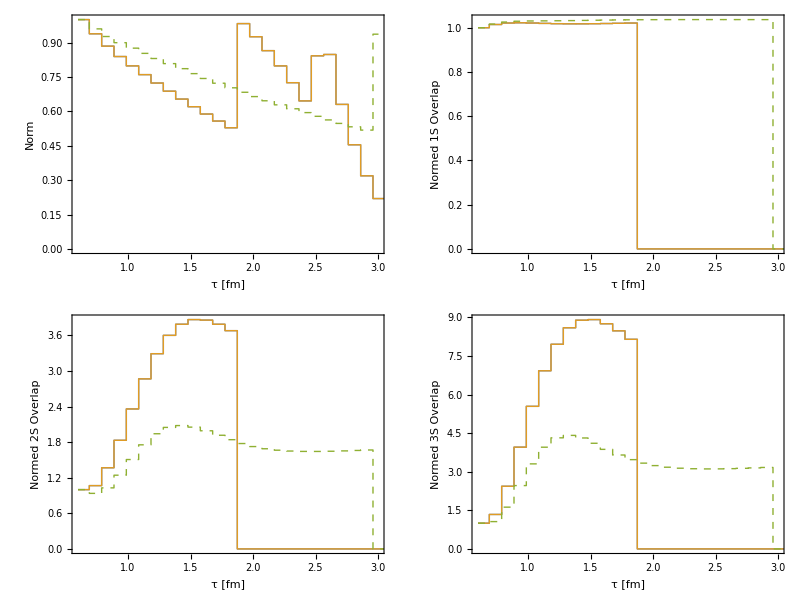

```mathematica
summaryPlot1[1]
```

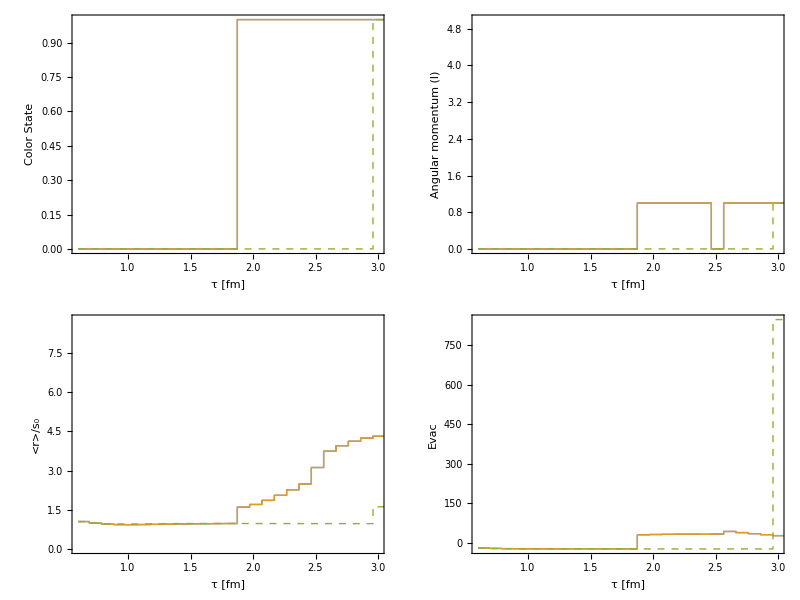

```mathematica
summaryPlot2[1]
```

```mathematica
myPlots = Table[summaryPlot1[traj],{traj,1,10,1}];
```

```mathematica
Manipulate[myPlots[[i]],{i,1,10,1}]
```

```mathematica
(*Export["animation.mp4",myPlots,"DisplayDurations"->.2];*)
```

```mathematica
myPlots2 = Table[summaryPlot2[traj],{traj,1,10,1}];
```

```mathematica
Manipulate[myPlots2[[i]],{i,1,10,1}]
```

```mathematica
Export["animation2.mp4",myPlots,"DisplayDurations"->.2];
```

## Summary plots - Delta with jumps (only LO)

```mathematica
summaryData0=Import[wd<>"/../output-0/summary.tsv"];
summaryData1=Import[wd<>"/../output-1/summary.tsv"];
grabColumn[x_,n_] := Transpose[{x[[All,1]],x[[All,n]]}]
grabNormedColumn[x_,n_] := Transpose[{x[[All,1]],x[[All,n]]/x[[All,n]][[1]]}]
```

```mathematica
keyVal =0.600071;
grabTrajectoryColumn[x_,n_,m_] := Module[{pos,data},
data=grabColumn[x,n];
pos=Drop[Position[data[[All,1]],keyVal],2]//Flatten;
pos=Take[pos,{m,m+1}];
pos[[2]] = pos[[2]]-1;
(*Print[pos];*)
Take[data,pos]
]
grabNormedTrajectoryColumn[x_,n_,m_] := Module[{pos,data},
data=grabNormedColumn[x,n];
pos=Drop[Position[data[[All,1]],keyVal],2]//Flatten;
pos=Take[pos,{m,m+1}];
pos[[2]] = pos[[2]]-1;
(*Print[pos];*)
Take[data,pos]
]
```

```mathematica
makePlot[col_,label_,traj_]:=ListPlot[{grabTrajectoryColumn[summaryData0,col,traj],grabTrajectoryColumn[summaryData1,col,traj](*,grabTrajectoryColumn[summaryData2,col,traj]*)},Joined->True,PlotStyle->{Thick,Thick,{Thick,Dashed}},(*PlotLegends->Placed[LineLegend[{"LO Suzuki-Trotter","LO Crank-Nicholson","NLO Crank-Nicholson"},LabelStyle->Directive[FontSize->14]],{Right,Top}],*)FrameLabel->{"τ [fm]",label},InterpolationOrder->0,PlotRange->{{0.6,3},All}]
makeNormedPlot[col_,label_,traj_]:=ListPlot[{grabNormedTrajectoryColumn[summaryData0,col,traj],grabNormedTrajectoryColumn[summaryData1,col,traj](*,grabNormedTrajectoryColumn[summaryData2,col,traj]*)},Joined->True,PlotStyle->{Thick,Thick,{Thick,Dashed}},(*PlotLegends->Placed[LineLegend[{"LO Suzuki-Trotter","LO Crank-Nicholson","NLO Crank-Nicholson"},LabelStyle->Directive[FontSize->14]],{Right,Top}],*)FrameLabel->{"τ [fm]",label},InterpolationOrder->0,PlotRange->{{0.6,3},All}]
```

```mathematica
summaryPlot1[traj_]:=Grid[{{makePlot[2,"Norm",traj],makeNormedPlot[5,"Normed 1S Overlap",traj]},{makeNormedPlot[6,"Normed 2S Overlap",traj],makeNormedPlot[8,"Normed 3S Overlap",traj]}}]
summaryPlot2[traj_]:=Grid[{{makePlot[3,"Color State",traj],makePlot[4,"Angular momentum (l)",traj]},{makePlot[11,"<r>/s_0",traj]}}]
```

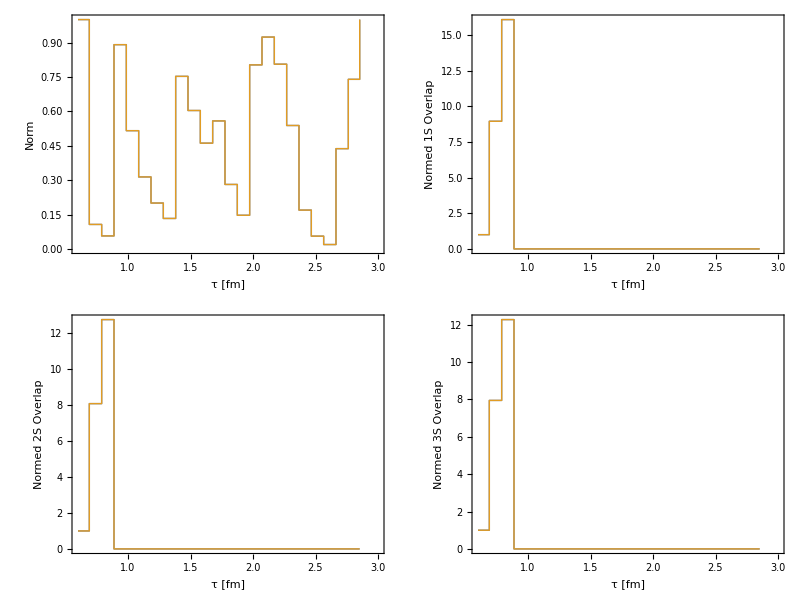

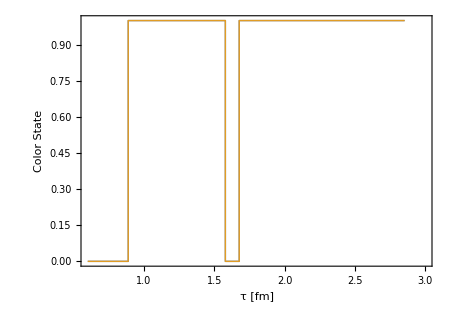
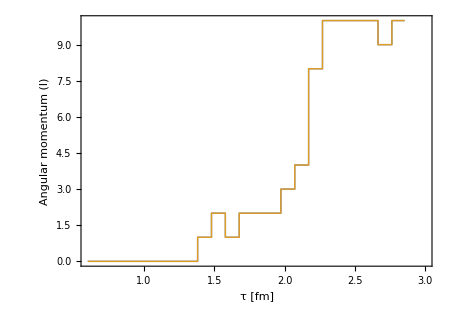
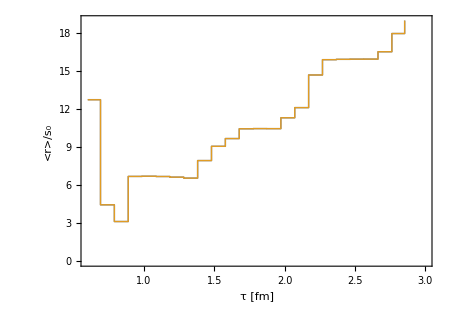
-Graphics- | -Graphics-
-Graphics- |

```mathematica
summaryPlot1[1]
summaryPlot2[1]
```

```mathematica
Manipulate[Grid[{{makePlot[4,"Angular momentum (l)",traj],makePlot[11,"<r>/s_0",traj]}}],{traj,1,95,1}]
```

```mathematica
Manipulate[summaryPlot1[traj],{traj,1,95,1}]
```

## Summary plots - Delta with jumps (wide Delta)

```mathematica
summaryData1=Import[wd<>"/../jumps/output-1/summary.tsv"];
summaryData2=Import[wd<>"/../jumps/output-2/summary.tsv"];
grabColumn[x_,n_] := Transpose[{x[[All,1]],x[[All,n]]}]
grabNormedColumn[x_,n_] := Transpose[{x[[All,1]],x[[All,n]]/x[[All,n]][[1]]}]
```

```mathematica
Length[summaryData1]
Length[summaryData2]
```

94533

95103

```mathematica
summaryData1[[1]]//Length
```

11

```mathematica
mapVal[x_] := Around[x[[1]],x[[2]]];
trajectoryAverage[x_,n_] := Module[{pos,pos2,data,len,m,out,md,ed},
data=grabColumn[x,n];
pos=Drop[Position[data[[All,1]],keyVal],2]//Flatten; (* find all plays where time = keyVal *)
len = Length[pos];
out= {};
pos2=Take[pos,{1,2}];
pos2[[2]] = pos2[[2]]-1;
times =Take[data[[All,1]],pos2];
For[m=1,m<len,m++,
pos2=Take[pos,{m,m+1}];
pos2[[2]] = pos2[[2]]-1;
out = AppendTo[out,Take[data[[All,2]],pos2]];
];
md=Mean/@Transpose[out];
ed = (StandardDeviation /@Transpose[out])/Sqrt[len-1];
Transpose[{times,mapVal/@Transpose[{md,ed}]}]
]
```

```mathematica
makePlot[col_,label_]:=ListPlot[{trajectoryAverage[summaryData1,col],trajectoryAverage[summaryData2,col]},Joined->True,PlotStyle->{Thick,Thick,{Thick,Dashed}},IntervalMarkers->"Bands",PlotLegends->Placed[LineLegend[{"LO","NLO"},LabelStyle->Directive[FontSize->14]],{Right,Top}],FrameLabel->{"τ [fm]",label},InterpolationOrder->1]
```

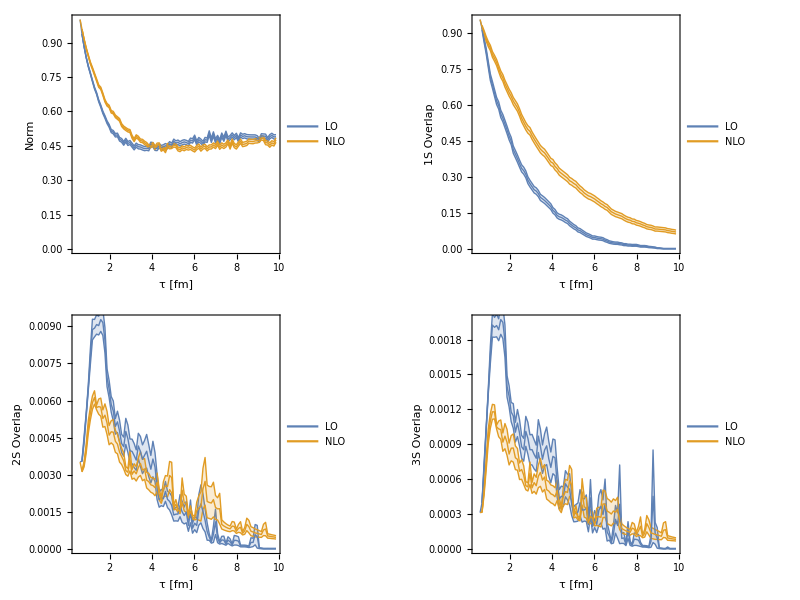

```mathematica
Grid[{{makePlot[2,"Norm"],
makePlot[5,"1S Overlap"]},{
makePlot[6,"2S Overlap"],
makePlot[8,"3S Overlap"]}}]
```

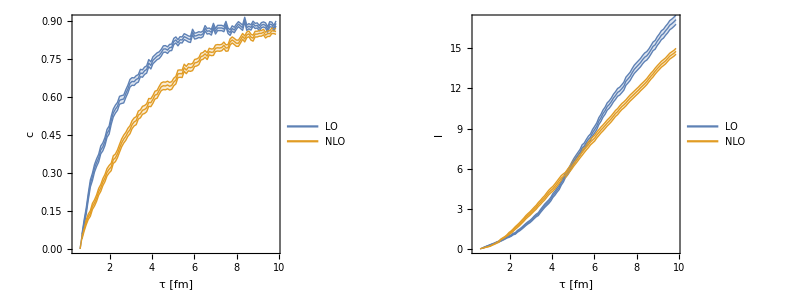

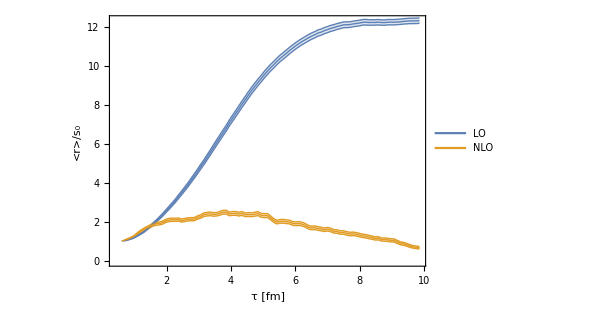

```mathematica
Grid[{{makePlot[3,"c"],makePlot[4,"l"]}}]
makePlot[11,"<r>/s_0"]
```

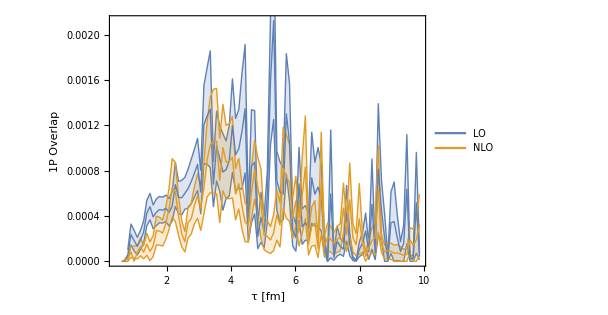

```mathematica
makePlot[10,"1P Overlap"]
```

### Compare with Heff

```mathematica
summaryDataHeff1=Import[wd<>"/../nojumps/output-1/summary.tsv"];
summaryDataHeff2=Import[wd<>"/../nojumps/output-2/summary.tsv"];
grabColumn[x_,n_] := Transpose[{x[[All,1]],x[[All,n]]}]
grabNormedColumn[x_,n_] := Transpose[{x[[All,1]],x[[All,n]]/x[[All,n]][[1]]}]
```

```mathematica
makePlotHeff[col_,label_]:=ListPlot[{grabColumn[summaryDataHeff1,col],grabColumn[summaryDataHeff2,col]},Joined->True,PlotStyle->{{Darker[Green],Thick,Dashed},{Red,Thick,Dashed}},PlotLegends->Placed[LineLegend[{"LO Heff","NLO Heff"},LabelStyle->Directive[FontSize->14]],{Right,Top}],FrameLabel->{"τ [fm]",label},PlotRange->All]
```

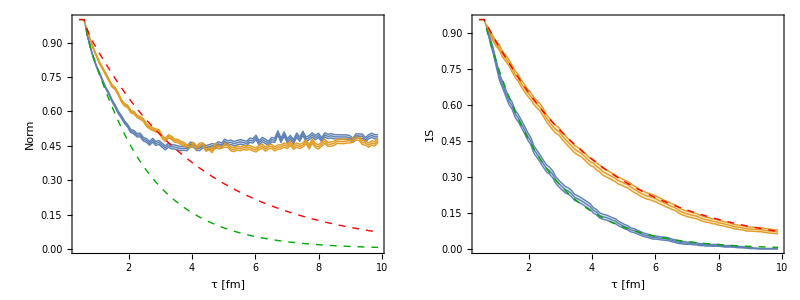

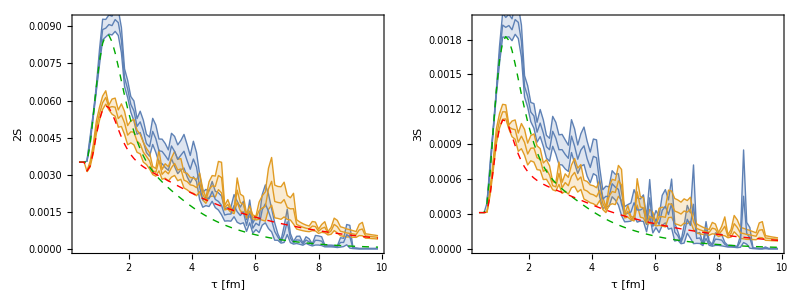

```mathematica
Grid[{{Show[makePlot[2,"Norm"],makePlotHeff[2,"Norm"]],Show[makePlot[5,"1S"],makePlotHeff[5,"1S"]]}}]
Grid[{{Show[makePlot[6,"2S"],makePlotHeff[6,"2S"]],Show[makePlot[8,"3S"],makePlotHeff[8,"3S"]]}}]
```

### Compare ratios

```mathematica
ratioData211=Take[Transpose[{times,trajectoryAverage[summaryData1,6][[All,2]]/trajectoryAverage[summaryData1,5][[All,2]]}],75];
ratioData212=Take[Transpose[{times,trajectoryAverage[summaryData2,6][[All,2]]/trajectoryAverage[summaryData2,5][[All,2]]}],75];
plot21=ListPlot[{ratioData211,ratioData212}];

ratioData211=Take[Transpose[{times,trajectoryAverage[summaryData1,8][[All,2]]/trajectoryAverage[summaryData1,5][[All,2]]}],75];
ratioData212=Take[Transpose[{times,trajectoryAverage[summaryData2,8][[All,2]]/trajectoryAverage[summaryData2,5][[All,2]]}],75];
plot31=ListPlot[{ratioData211,ratioData212}];
```

```mathematica
makeRatio[x_,n1_,n2_]:=Transpose[{grabColumn[x,n1][[All,1]],grabColumn[x,n1][[All,2]]/grabColumn[x,n2][[All,2]]}]
```

```mathematica
plot21h=ListPlot[{makeRatio[summaryDataHeff1,6,5],makeRatio[summaryDataHeff2,6,5]},Joined->True,PlotStyle->{{Thick,Dashed}},PlotLegends->Placed[LineLegend[{"LO Crank-Nicholson","NLO Crank-Nicholson"},LabelStyle->Directive[FontSize->14]],{Right,Top}],FrameLabel->{"τ [fm]","ratio"},PlotRange->All];
plot31h=ListPlot[{makeRatio[summaryDataHeff1,8,5],makeRatio[summaryDataHeff2,8,5]},Joined->True,PlotStyle->{{Thick,Dashed}},PlotLegends->Placed[LineLegend[{"LO Crank-Nicholson","NLO Crank-Nicholson"},LabelStyle->Directive[FontSize->14]],{Right,Top}],FrameLabel->{"τ [fm]","ratio"},PlotRange->All];
```

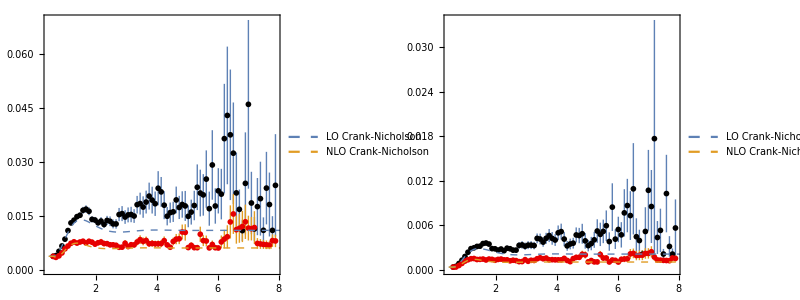

```mathematica
Grid[{{Show[plot21,plot21h],
Show[plot31,plot31h]}}]
```

```mathematica
Exp[-(9.4-9)/0.425]
```

0.390169

## Summary plots - Delta with jumps (New summary.tsv Format)

```mathematica
(*summaryDataRaw1=Import[wd<>"/../jumps/output-osc-1/summaries.gz"];
summaryDataRaw2=Import[wd<>"/../jumps/output-osc-2/summaries.gz"];*)
```

```mathematica
summaryDataRaw1=Import[wd<>"/../output-0/summary.tsv"];
summaryDataRaw2=Import[wd<>"/../output-2/summary.tsv"];
```

```mathematica
keyVal =0.600071;
keyVal =0.600012;
extractData[x_] := Module[{pos,pos2,len,dataOut,m},
(*pos=Join[Position[x[[All,1]],keyVal]//Flatten,{Length[x]+1}];*)
pos=Position[x[[All,1]],keyVal]//Flatten;
len = Length[pos];
dataOut = {};
For[m=1,m<len,m++,
pos2=Take[pos,{m,m+1}];
pos2[[2]] = pos2[[2]]-1;
AppendTo[dataOut,Take[x,pos2]];
];
len = Length[dataOut];
avgData=(Mean/@Transpose[dataOut]) //N;
errData=(StandardDeviation/@Transpose[dataOut])/Sqrt[len] //N;
Table[Around[avgData[[i,j]],errData[[i,j]]],{i,1,Length[avgData]},{j,1,Length[avgData[[1]]]}]
]
```

```mathematica
summaryData1 = extractData[summaryDataRaw1];
times=summaryData1[[All,1]];
```

```mathematica
summaryData2 = extractData[summaryDataRaw2];
```

```mathematica
makePlot[col_,label_]:=ListPlot[{summaryData1[[All,{1,col}]],summaryData2[[All,{1,col}]]},Joined->True,PlotStyle->{Thick,Thick,{Thick,Dashed}},IntervalMarkers->"Bands",PlotRange->All,PlotLegends->Placed[LineLegend[{"LO","NLO"},LabelStyle->Directive[FontSize->14]],{Right,Top}],FrameLabel->{"τ [fm]",label},InterpolationOrder->0,ImageSize->500]
makeLogPlot[col_,label_]:=ListLogPlot[{summaryData1[[All,{1,col}]],summaryData2[[All,{1,col}]]},Joined->True,PlotStyle->{Thick,Thick,{Thick,Dashed}},IntervalMarkers->"Bands",PlotLegends->Placed[LineLegend[{"LO","NLO"},LabelStyle->Directive[FontSize->14]],{Right,Top}],FrameLabel->{"τ [fm]",label},InterpolationOrder->0,ImageSize->500,PlotRange->{10^(-7),Automatic}]
```

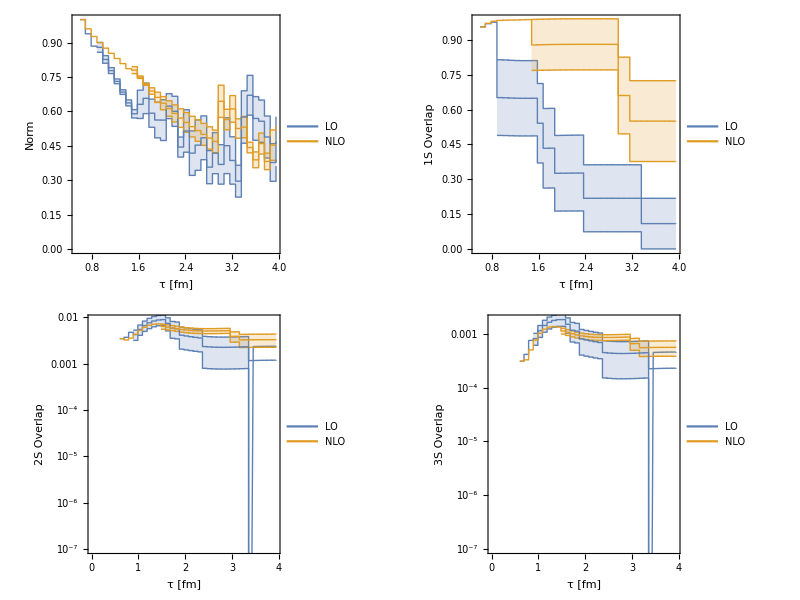

```mathematica
Grid[{{makePlot[2,"Norm"],
makePlot[5,"1S Overlap"]},{
makeLogPlot[6,"2S Overlap"],
makeLogPlot[8,"3S Overlap"]}}]
```

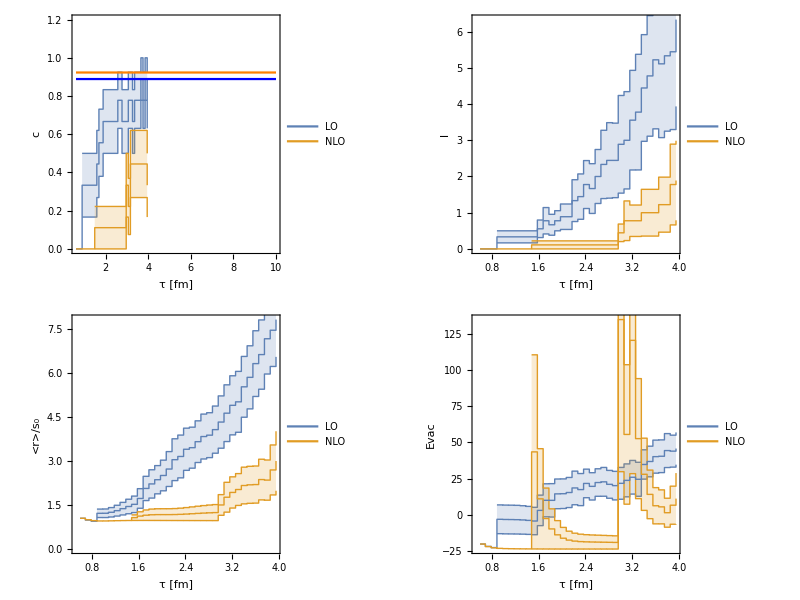

```mathematica
tPlot=Plot[8/9,{t,0.6,10},PlotStyle->{Blue}];
tPlot2=Plot[12/13,{t,0.6,10},PlotStyle->{Orange}];
Grid[{{Show[makePlot[3,"c"],tPlot,tPlot2,PlotRange->{0,1.2}],makePlot[4,"l"]},{makePlot[11,"<r>/s_0"],makePlot[12,"Evac"]}}]
```

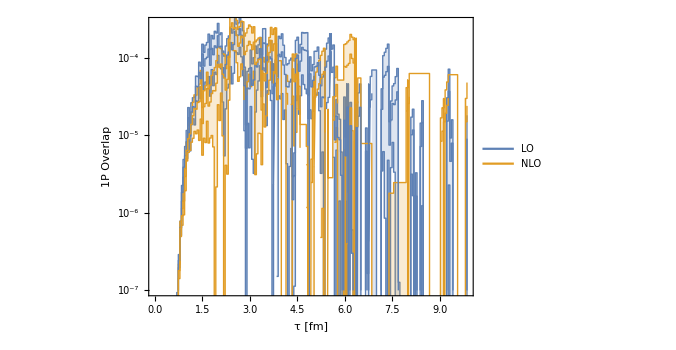
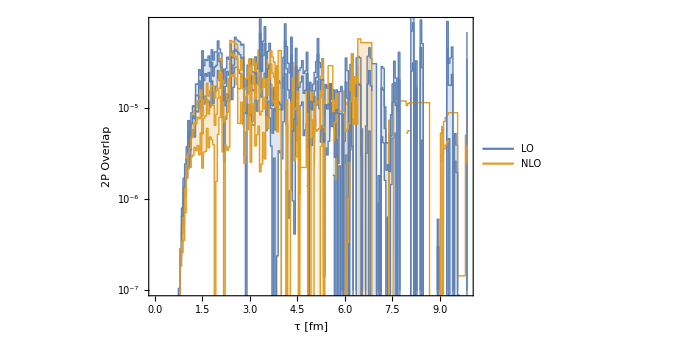
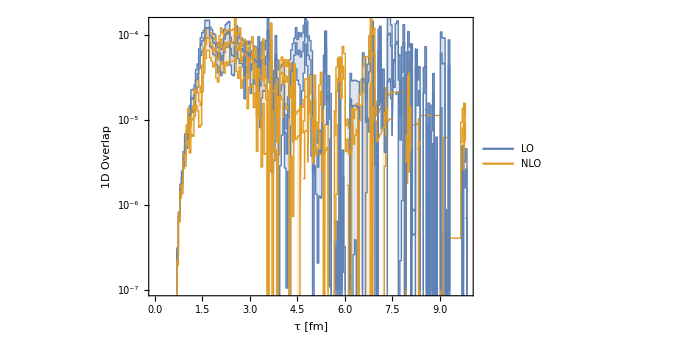
-Graphics- | -Graphics-
-Graphics- |

```mathematica
Grid[{{makeLogPlot[7,"1P Overlap"],makeLogPlot[9,"2P Overlap"]},{makeLogPlot[10,"1D Overlap"]}}]
```

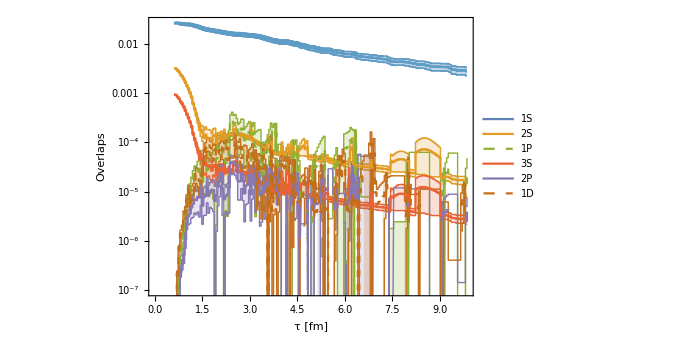

```mathematica
ListLogPlot[{summaryData2[[All,{1,5}]],summaryData2[[All,{1,6}]],summaryData2[[All,{1,7}]],summaryData2[[All,{1,8}]],summaryData2[[All,{1,9}]],summaryData2[[All,{1,10}]],summaryData2[[All,{1,5}]]},Joined->True,PlotStyle->{Thick,Thick,{Thick,Dashed}},IntervalMarkers->"Bands",PlotLegends->Placed[LineLegend[{"1S","2S","1P","3S","2P","1D"},LabelStyle->Directive[FontSize->14]],Right],FrameLabel->{"τ [fm]","Overlaps"},InterpolationOrder->0,ImageSize->500,PlotRange->{10^(-7),Automatic}]
```

### Compare with Heff

```mathematica
summaryDataHeff1=Import[wd<>"/../nojumps/output-1/summary.tsv"];
summaryDataHeff2=Import[wd<>"/../nojumps/output-2/summary.tsv"];
grabColumn[x_,n_] := Transpose[{x[[All,1]],x[[All,n]]}]
grabNormedColumn[x_,n_] := Transpose[{x[[All,1]],x[[All,n]]/x[[All,n]][[1]]}]
```

```mathematica
makePlotHeff[col_,label_]:=ListPlot[{grabColumn[summaryDataHeff1,col],grabColumn[summaryDataHeff2,col]},Joined->True,PlotStyle->{{Darker[Blue],Thick,Dashed},{Red,Thick,Dashed}},PlotLegends->Placed[LineLegend[{"LO Heff","NLO Heff"},LabelStyle->Directive[FontSize->14]],{Right,Top}],FrameLabel->{"τ [fm]",label},PlotRange->All]
makeLogPlotHeff[col_,label_]:=ListLogPlot[{grabColumn[summaryDataHeff1,col],grabColumn[summaryDataHeff2,col]},Joined->True,PlotStyle->{{Darker[Blue],Thick,Dashed},{Red,Thick,Dashed}},PlotLegends->Placed[LineLegend[{"LO Heff","NLO Heff"},LabelStyle->Directive[FontSize->14]],{Right,Top}],FrameLabel->{"τ [fm]",label},PlotRange->{10^(-7),0.005}]
```

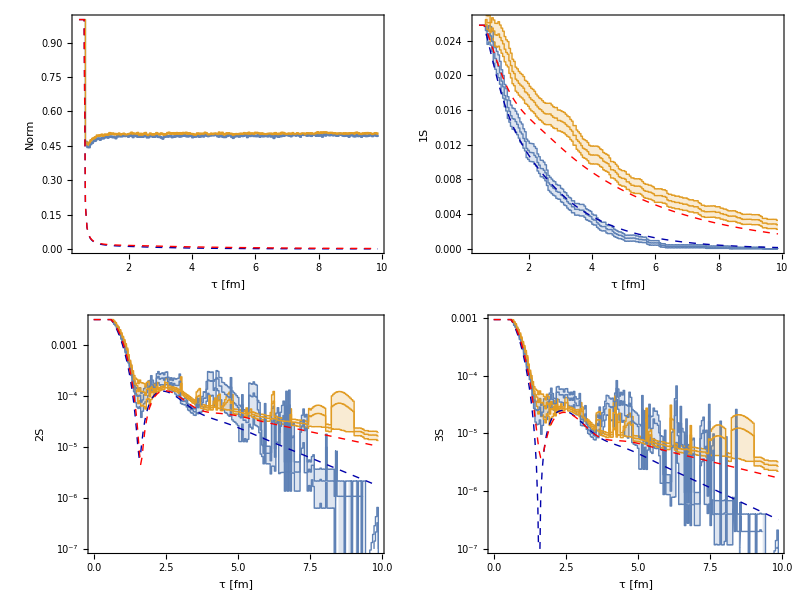

```mathematica
Grid[{{Show[makePlot[2,"Norm"],makePlotHeff[2,"Norm"]],Show[makePlot[5,"1S"],makePlotHeff[5,"1S"]]},{Show[makeLogPlot[6,"2S"],makeLogPlotHeff[6,"2S"]],Show[makeLogPlot[8,"3S"],makeLogPlotHeff[8,"3S"]]}}]
```

### Compare ratios

```mathematica
clip = 189;
```

```mathematica
ratioData211=Take[Transpose[{times,summaryData1[[All,{1,6}]][[All,2]]/summaryData1[[All,{1,5}]][[All,2]]}],clip];
ratioData212=Take[Transpose[{times,summaryData2[[All,{1,6}]][[All,2]]/summaryData2[[All,{1,5}]][[All,2]]}],clip];plot21=ListPlot[{ratioData211,ratioData212},FrameLabel->{"τ [fm]","P(2S)/P(1S)"},IntervalMarkers->"Bars",PlotRange->Automatic,ImageSize->550];

ratioData211=Take[Transpose[{times,summaryData1[[All,{1,8}]][[All,2]]/summaryData1[[All,{1,5}]][[All,2]]}],clip];
ratioData212=Take[Transpose[{times,summaryData2[[All,{1,8}]][[All,2]]/summaryData2[[All,{1,5}]][[All,2]]}],clip];plot31=ListPlot[{ratioData211,ratioData212},FrameLabel->{"τ [fm]","P(3S)/P(1S)"},IntervalMarkers->"Bars",PlotRange->Automatic,ImageSize->550];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

```mathematica
summaryDataHeff1=Import[wd<>"/../nojumps/output-1/summary.tsv"];
summaryDataHeff2=Import[wd<>"/../nojumps/output-2/summary.tsv"];
grabColumn[x_,n_] := Transpose[{x[[All,1]],x[[All,n]]}]
grabNormedColumn[x_,n_] := Transpose[{x[[All,1]],x[[All,n]]/x[[All,n]][[1]]}]
```

```mathematica
makeRatio[x_,n1_,n2_]:=Transpose[{grabColumn[x,n1][[All,1]],grabColumn[x,n1][[All,2]]/grabColumn[x,n2][[All,2]]}]
```

```mathematica
makeRatio[summaryDataHeff1,6,5][[-1]]
makeRatio[summaryDataHeff2,6,5][[-1]]
```

{9.86635,0.0108655}

{9.86635,0.00598026}

```mathematica
plot21h=ListPlot[{makeRatio[summaryDataHeff1,6,5],makeRatio[summaryDataHeff2,6,5]},Joined->True,PlotStyle->{{Thick,Dashed}},PlotLegends->Placed[LineLegend[{"LO Crank-Nicholson","NLO Crank-Nicholson"},LabelStyle->Directive[FontSize->14]],{Left,Bottom}],FrameLabel->{"τ [fm]","ratio"},PlotRange->Automatic];
plot31h=ListPlot[{makeRatio[summaryDataHeff1,8,5],makeRatio[summaryDataHeff2,8,5]},Joined->True,PlotStyle->{{Thick,Dashed}},PlotLegends->Placed[LineLegend[{"LO Crank-Nicholson","NLO Crank-Nicholson"},LabelStyle->Directive[FontSize->14]],{Left,Bottom}],FrameLabel->{"τ [fm]","ratio"},PlotRange->Automatic];
```

```mathematica
Grid[{{Show[plot21,plot21h],Show[plot31,plot31h]}}]
```

-Graphics-

Expectation for 2 s

```mathematica
Exp[-(9.3449-8.99968)/0.425]
```

0.443844

## Summary plots - Delta with jumps (New summary.tsv Format - WIDE)

```mathematica
(*summaryDataRaw1=Import[wd<>"/../jumps/output-osc-1/summaries.gz"];*)
```

```mathematica
summaryDataRaw1=Import[wd<>"/../jumps/output-osc-1-long/summaries.gz"];
summaryDataRaw2=Import[wd<>"/../jumps/output-osc-2-long/summaries.gz"];
```

```mathematica
keyVal =0.600071;
selectByLen[x_,len_] := Select[x,Length[#]==len&]
extractData[x_] := Module[{pos,pos2,len,dataOut,m},
pos=Join[Position[x[[All,1]],keyVal]//Flatten,{Length[x]+1}];
len = Length[pos];
dataOut = {};
For[m=1,m<len,m++,
pos2=Take[pos,{m,m+1}];
pos2[[2]] = pos2[[2]]-1;
AppendTo[dataOut,Take[x,pos2]];
];
dataOut = selectByLen[dataOut,Length[ dataOut[[1]] ] ];
len = Length[dataOut];
Print[len];
avgData=(Mean/@Transpose[dataOut]) //N;
errData=(StandardDeviation/@Transpose[dataOut])/Sqrt[len] //N;
Table[Around[avgData[[i,j]],errData[[i,j]]],{i,1,Length[avgData]},{j,1,Length[avgData[[1]]]}]
]
```

```mathematica
summaryData1 = extractData[summaryDataRaw1];
```

10000

```mathematica
summaryData2 = extractData[summaryDataRaw2];
```

9997

```mathematica
times=summaryData2[[All,1]];
```

```mathematica
makePlot[col_,label_]:=ListPlot[{summaryData1[[All,{1,col}]],summaryData2[[All,{1,col}]]},Joined->True,PlotStyle->{Thick,Thick,{Thick,Dashed}},IntervalMarkers->"Bands",PlotRange->All,PlotLegends->Placed[LineLegend[{"LO","NLO"},LabelStyle->Directive[FontSize->14]],{Right,Top}],FrameLabel->{"τ [fm]",label},InterpolationOrder->1,ImageSize->500]
makeLogPlot[col_,label_]:=ListLogPlot[{summaryData1[[All,{1,col}]],summaryData2[[All,{1,col}]]},Joined->True,PlotStyle->{Thick,Thick,{Thick,Dashed}},IntervalMarkers->"Bands",PlotLegends->Placed[LineLegend[{"LO","NLO"},LabelStyle->Directive[FontSize->14]],{Right,Top}],FrameLabel->{"τ [fm]",label},InterpolationOrder->1,ImageSize->500,PlotRange->{10^(-7),Automatic}]
```

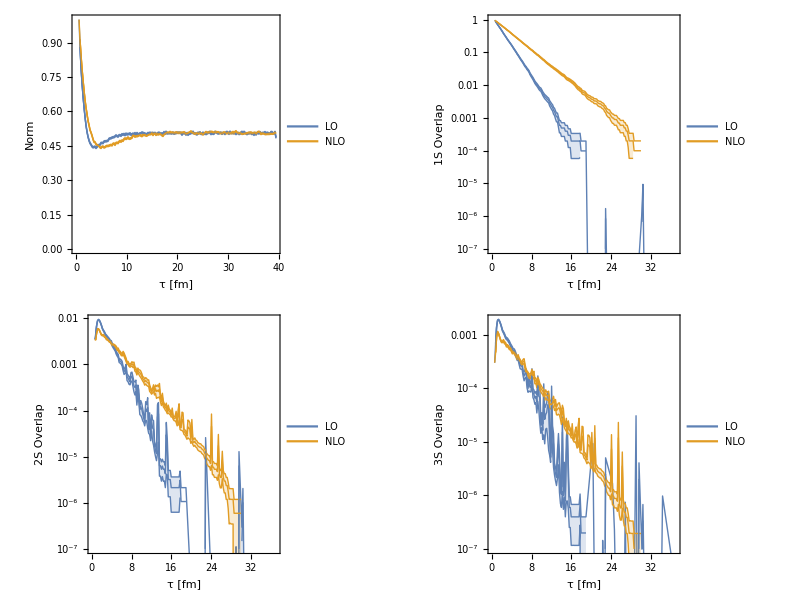

```mathematica
Grid[{{makePlot[2,"Norm"],
makeLogPlot[5,"1S Overlap"]},{
makeLogPlot[6,"2S Overlap"],
makeLogPlot[8,"3S Overlap"]}}]
```

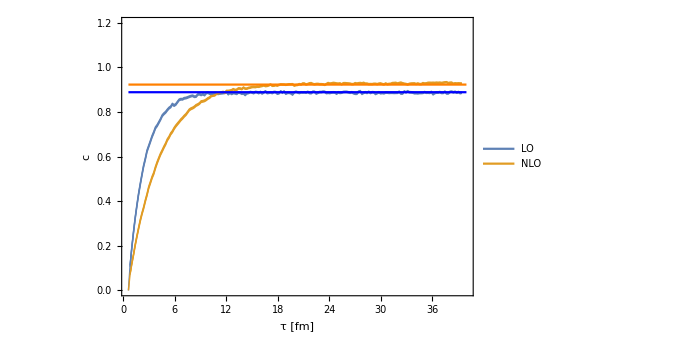
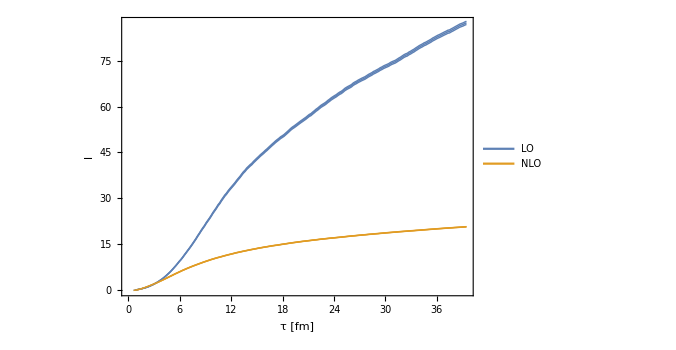
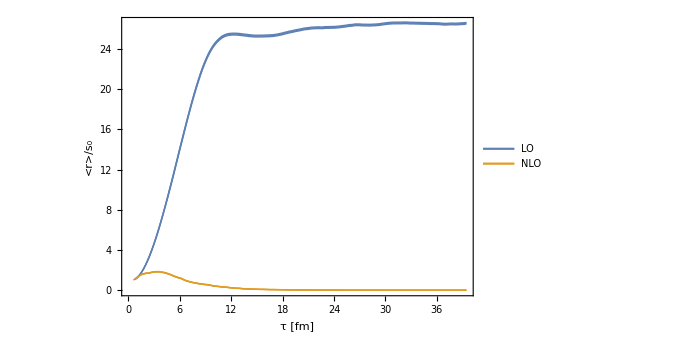
-Graphics- | -Graphics-
-Graphics- |

```mathematica
tPlot=Plot[8/9,{t,0.6,40},PlotStyle->{Blue}];
tPlot2=Plot[12/13,{t,0.6,40},PlotStyle->{Orange}];
Grid[{{Show[makePlot[3,"c"],tPlot,tPlot2,PlotRange->{0,1.2}],makePlot[4,"l"]},{makePlot[11,"<r>/s_0"]}}]
```

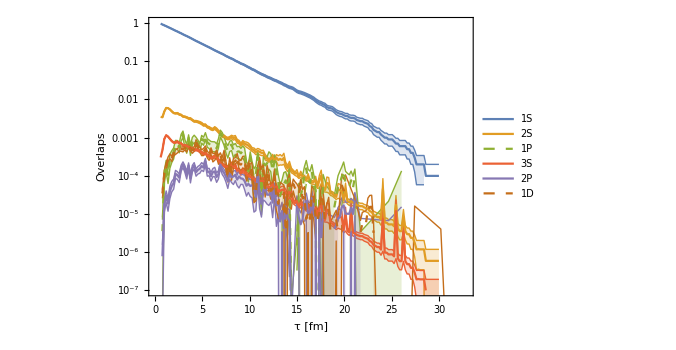

```mathematica
ListLogPlot[{summaryData2[[All,{1,5}]],summaryData2[[All,{1,6}]],summaryData2[[All,{1,7}]],summaryData2[[All,{1,8}]],summaryData2[[All,{1,9}]],summaryData2[[All,{1,10}]]},Joined->True,PlotStyle->{Thick,Thick,{Thick,Dashed}},IntervalMarkers->"Bands",PlotLegends->Placed[LineLegend[{"1S","2S","1P","3S","2P","1D"},LabelStyle->Directive[FontSize->14]],Right],FrameLabel->{"τ [fm]","Overlaps"},InterpolationOrder->1,ImageSize->500,PlotRange->{10^(-7),Automatic}]
```

### Compare with Heff

```mathematica
summaryDataHeff1=Import[wd<>"/../nojumps/output-osc-wide-1/summary.tsv"];
summaryDataHeff2=Import[wd<>"/../nojumps/output-osc-wide-2/summary.tsv"];
grabColumn[x_,n_] := Transpose[{x[[All,1]],x[[All,n]]}]
grabNormedColumn[x_,n_] := Transpose[{x[[All,1]],x[[All,n]]/x[[All,n]][[1]]}]
```

```mathematica
makePlotHeff[col_,label_]:=ListPlot[{grabColumn[summaryDataHeff1,col],grabColumn[summaryDataHeff2,col]},Joined->True,PlotStyle->{{Darker[Blue],Thick,Dashed},{Red,Thick,Dashed}},PlotLegends->Placed[LineLegend[{"LO Heff","NLO Heff"},LabelStyle->Directive[FontSize->14]],{Right,Top}],FrameLabel->{"τ [fm]",label},PlotRange->All]
makeLogPlotHeff[col_,label_]:=ListLogPlot[{grabColumn[summaryDataHeff1,col],grabColumn[summaryDataHeff2,col]},Joined->True,PlotStyle->{{Darker[Blue],Thick,Dashed},{Red,Thick,Dashed}},PlotLegends->Placed[LineLegend[{"LO Heff","NLO Heff"},LabelStyle->Directive[FontSize->14]],{Right,Top}],FrameLabel->{"τ [fm]",label}]
```

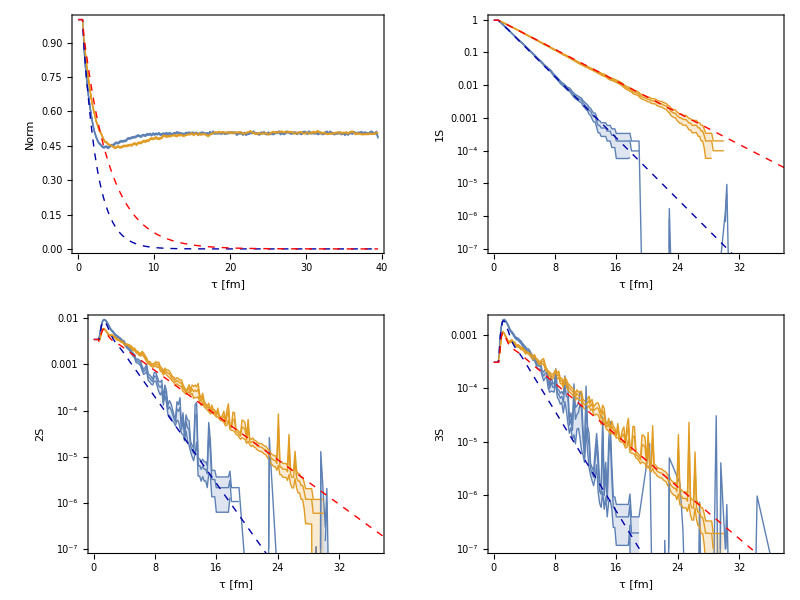

```mathematica
Grid[{{Show[makePlot[2,"Norm"],makePlotHeff[2,"Norm"]],Show[makeLogPlot[5,"1S"],makeLogPlotHeff[5,"1S"]]},{Show[makeLogPlot[6,"2S"],makeLogPlotHeff[6,"2S"]],Show[makeLogPlot[8,"3S"],makeLogPlotHeff[8,"3S"]]}}]
```

### Compare ratios

```mathematica
clip = 150;
```

```mathematica
summaryData2[[All,{1,6}]][[All,2]] //Length
```

198

```mathematica
ratioData211=Take[Transpose[{times,summaryData1[[All,{1,6}]][[All,2]]/summaryData1[[All,{1,5}]][[All,2]]}],clip];
ratioData212=Take[Transpose[{times,summaryData2[[All,{1,6}]][[All,2]]/summaryData2[[All,{1,5}]][[All,2]]}],clip];plot21=ListPlot[{ratioData211,ratioData212},FrameLabel->{"τ [fm]","P(2S)/P(1S)"},IntervalMarkers->"Bars",PlotRange->Automatic,ImageSize->550];

ratioData211=Take[Transpose[{times,summaryData1[[All,{1,8}]][[All,2]]/summaryData1[[All,{1,5}]][[All,2]]}],clip];
ratioData212=Take[Transpose[{times,summaryData2[[All,{1,8}]][[All,2]]/summaryData2[[All,{1,5}]][[All,2]]}],clip];plot31=ListPlot[{ratioData211,ratioData212},FrameLabel->{"τ [fm]","P(3S)/P(1S)"},IntervalMarkers->"Bars",PlotRange->Automatic,ImageSize->550];
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
summaryDataHeff1=Import[wd<>"/../nojumps/output-osc-wide-1/summary.tsv"];
summaryDataHeff2=Import[wd<>"/../nojumps/output-osc-wide-2/summary.tsv"];
grabColumn[x_,n_] := Transpose[{x[[All,1]],x[[All,n]]}]
grabNormedColumn[x_,n_] := Transpose[{x[[All,1]],x[[All,n]]/x[[All,n]][[1]]}]
```

```mathematica
makeRatio[x_,n1_,n2_]:=Transpose[{grabColumn[x,n1][[All,1]],grabColumn[x,n1][[All,2]]/grabColumn[x,n2][[All,2]]}]
```

```mathematica
makeRatio[summaryDataHeff1,6,5][[-1]]
makeRatio[summaryDataHeff2,6,5][[-1]]
```

{39.4654,0.0108581}

{39.4654,0.00597506}

```mathematica
makeRatio[summaryDataHeff2,8,5][[-1]]
```

{39.4654,0.00100535}

```mathematica
plot21h=ListPlot[{makeRatio[summaryDataHeff1,6,5],makeRatio[summaryDataHeff2,6,5]},Joined->True,PlotStyle->{{Thick,Dashed}},PlotLegends->Placed[LineLegend[{"LO Crank-Nicholson","NLO Crank-Nicholson"},LabelStyle->Directive[FontSize->14]],{Left,Bottom}],FrameLabel->{"τ [fm]","ratio 2/1"},PlotRange->Automatic];
plot31h=ListPlot[{makeRatio[summaryDataHeff1,8,5],makeRatio[summaryDataHeff2,8,5]},Joined->True,PlotStyle->{{Thick,Dashed}},PlotLegends->Placed[LineLegend[{"LO Crank-Nicholson","NLO Crank-Nicholson"},LabelStyle->Directive[FontSize->14]],{Left,Bottom}],FrameLabel->{"τ [fm]","ratio 3/1"},PlotRange->Automatic];
```

```mathematica
Grid[{{Show[plot21,plot21h],Show[plot31,plot31h]}}]
```

-Graphics-

Expectation for 2S

```mathematica
Exp[-(9.3449-8.99968)/0.425]
```

0.443844

Expectation for 3S

```mathematica
Exp[-(9.40899-8.99968)/0.425]
```

0.381714